## STAT 333 Project 3 Iris Zhang (jxz971)

### Problem 1

#### Simulate sums of independent Cauchy random quantities but normalize them by n^-1 and n^(-3/2)instead of the usual SFL √n. Draw the corresponding histograms. Comment on what you see.

```mathematica
n=10000;
```

```mathematica
theta=RandomReal[{-Pi/2,Pi/2},1000];
y=Tan[Pi*(theta-0.5)];
```

Normalization using n^-1 shows below:

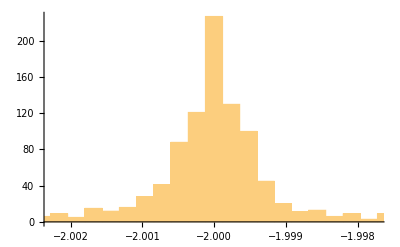

```mathematica
SFL1 =Table[((y[[i]]-n*0.5)/N[n*0.25]),{i,1000}];
His1=Histogram[SFL1]
```

Normalization using n^(-3/2) shows below:

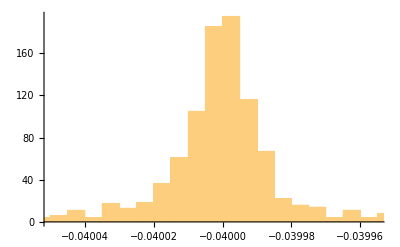

```mathematica
SFL2=Table[((y[[i]]-n*0.5)/N[(n*0.25)^1.5]),{i,1000}];
His2=Histogram[SFL2]
```

From the two graphs above, we can see that the overall distributions are the same while the mean of them are different.

### Problem 2

#### Implement the Kolmogorov-Smirnov test of fit for the exponential distribution (find its mean first) and the water drops data contained in the file DROPS located on the UVW Web Site. Do the Q-Q plots as well.

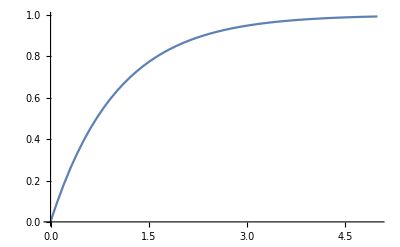

```mathematica
xx=RandomReal[{0,1},1000];
yy=Table[-Log[1-xx[[i]]],{i,1,1000}];
Meanyy=Mean[yy];
Stdyy=StandardDeviation[yy];
Lambda=1/Meanyy;
CDFex=CDF[ExponentialDistribution[Lambda],x];
CDF1=Plot[CDFex,{x,0,5}]
```

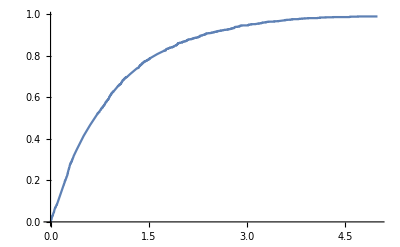

```mathematica
ff[x_]:=Sum[If[x<yy[[i]],0,1],{i,1,Length[yy]}]/Length[yy]
CDF2=Plot[ff[x],{x,0,5}]
```

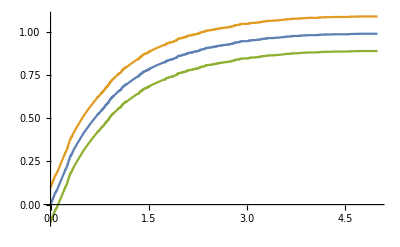

```mathematica
CDF3=Plot[{ff[x],ff[x]+0.1,ff[x]-0.1},{x,0,5}]
```

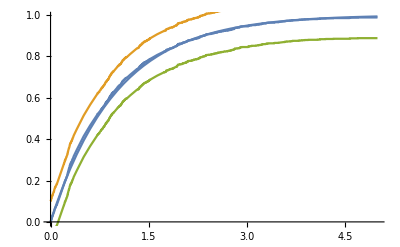

```mathematica
Show[CDF1,CDF3]
```

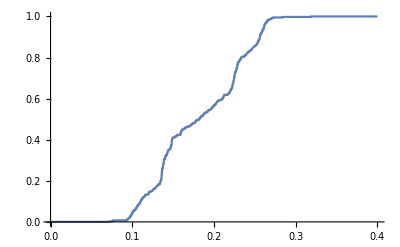

```mathematica
Drp={0.18228360,0.18623970,0.13423350,0.10354810,0.15513900,0.23274050,0.20233310,0.12894790,0.18684980,0.22657810,0.26112470,0.19178580,0.13767700,0.14837620,0.22277630,0.16055710,0.13788350,0.09521610,0.24578210,0.17383130,0.25812850,0.18938570,0.25420280,0.22464200,0.26155470,0.10953020,0.22034160,0.10145990,0.19693630,0.12816710,0.13596500,0.10053220,0.25587460,0.14042210,0.25563470,0.13526800,0.25192090,0.25315870,0.25650260,0.07200480,0.22221230,0.10651970,0.23083320,0.14309380,0.12039200,0.07573480,0.28357910,0.13409110,0.25356630,0.13608820,0.15960660,0.20411740,0.25443260,0.10519020,0.22459810,0.10852200,0.23142460,0.18760390,0.14815410,0.13764410,0.22559380,0.14294190,0.21218650,0.12436990,0.17052370,0.26370070,0.22443330,0.13576010,0.22104630,0.14850460,0.20739950,0.23946950,0.09949950,0.13500100,0.22572200,0.13560920,0.26428920,0.16429840,0.13426580,0.21094650,0.22839840,0.13847070,0.22873960,0.09668840,0.21728640,0.21903800,0.14815920,0.13720790,0.22385060,0.13849930,0.25677440,0.14003500,0.13574610,0.21009840,0.22764460,0.13569010,0.23362570,0.10627020,0.20359420,0.22037170,0.14801240,0.14313470,0.22738740,0.13893190,0.26134080,0.15902480,0.13821110,0.25994540,0.19984440,0.13702970,0.25571080,0.10017000,0.24149470,0.20942150,0.09821050,0.17724780,0.22568230,0.09987190,0.25377520,0.13363160,0.14934250,0.25567830,0.16646210,0.13653430,0.26081120,0.11141880,0.22362140,0.26196300,0.25485620,0.15926790,0.22449670,0.11083920,0.22594470,0.14749760,0.09495230,0.13961280,0.22764470,0.14142230,0.24807480,0.13791740,0.24859080,0.25935050,0.26436380,0.14695130,0.23698890,0.10994630,0.24675460,0.19712410,0.10504020,0.11948800,0.22092570,0.13606610,0.22484940,0.12570890,0.16141710,0.26257510,0.14825630,0.13100610,0.20236200,0.13893380,0.26028230,0.23129920,0.09723730,0.24600470,0.23302040,0.14716670,0.18991060,0.09395180,0.14256570,0.25940860,0.13184190,0.14779980,0.26544610,0.17659160,0.25689390,0.22272640,0.10381410,0.22347600,0.25889310,0.09551590,0.21917120,0.07637890,0.14582530,0.27091080,0.13431580,0.11580080,0.26142020,0.13817780,0.25436520,0.19498570,0.09923730,0.22391340,0.22166680,0.09870400,0.22214220,0.14858030,0.17792490,0.24428880,0.14327470,0.15278630,0.25635740,0.14497800,0.18314970,0.23344810,0.11068690,0.26540170,0.14857800,0.10705320,0.22829050,0.18691300,0.13606300,0.25154320,0.10921350,0.22934640,0.22450430,0.13692630,0.23764460,0.18372960,0.10921790,0.19986190,0.15007520,0.13633160,0.22506690,0.11534350,0.17324380,0.21237050,0.14873530,0.21643160,0.22657440,0.13686960,0.23828540,0.318174320,0.14837860,0.21115580,0.16123000,0.13529380,0.24016030,0.12552070,0.15950540,0.21113940,0.14725600,0.21805820,0.22875220,0.12800870,0.20448610,0.21948410,0.14692220,0.24746870,0.14248680,0.13871530,0.23005070,0.16313400,0.13891430,0.26708190,0.11291010,0.25614080,0.24051200,0.24548400,0.23622310,0.23961130,0.09302900,0.21150500,0.11970740,0.12498680,0.11555500,0.13855050,0.12045270,0.26194240,0.14797380,0.16864190,0.22269730,0.26032830,0.25778280,0.22254430,0.10020850,0.26106870,0.15855650,0.14371780,0.11136020,0.12119620,0.14110830,0.25684420,0.09828760,0.23301490,0.20504970,0.18349520,0.21975910,0.24160800,0.10200310,0.21208000,0.14020810,0.15974330,0.18873760,0.14236020,0.12082240,0.22755640,0.14818550,0.22244030,0.17957990,0.24217980,0.20160190,0.22291860,0.14020770,0.25848130,0.13665170,0.17852080,0.11437730,0.15921670,0.13596970,0.26868740,0.10135420,0.22488520,0.20168690,0.20958320,0.22973200,0.22528830,0.10985200,0.25246890,0.14021050,0.17207190,0.14624990,0.14421290,0.13553570,0.19721490,0.11316860,0.22365350,0.19277550,0.22177710,0.22281810,0.22673220,0.18224740,0.22948630,0.13615970,0.14343280,0.13595380,0.13332310,0.13758030,0.17235540,0.13477980,0.22750740,0.27205230,0.22723570,0.22356740,0.26976620,0.16408940,0.25041400,0.13610470,0.09729680,0.10675350,0.14689520,0.10447090,0.19264200,0.11169570,0.25101950,0.24382670,0.25675530,0.23134120,0.19872520,0.15405980,0.26169180,0.12361070,0.11594210,0.13849870,0.12892750,0.15996210,0.18149290,0.10359830,0.20306880,0.22509590,0.22510400,0.22840200,0.24895140,0.19837270,0.25859040,0.18603360,0.13769650,0.13587430,0.13107450,0.12671680,0.17744900,0.10807120,0.15458710,0.22524160,0.22834810,0.26317470,0.25623170,0.14897020,0.25305620,0.19255750,0.13608600,0.13614730,0.11293430,0.13007420,0.16590880,0.10560190,0.19604770,0.22842020,0.22890840,0.19967150,0.17581550,0.21840620,0.26584180,0.18360270,0.13641250,0.15187060,0.17108980};
MeanDrp=Mean[Drp];
StdDrp=StandardDeviation[Drp];
LambdaDrp=1/MeanDrp;
fff[x_]:=Sum[If[x<Drp[[i]],0,1],{i,1,Length[Drp]}]/Length[Drp]
CDF4=Plot[fff[x],{x,0,.4}]
```

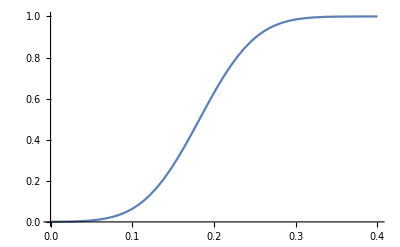

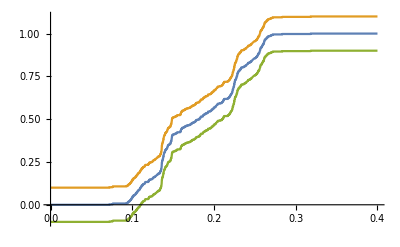

```mathematica
fffz=CDF[NormalDistribution[MeanDrp,StdDrp],x];
CDF5=Plot[fffz,{x,0,.4}]
CDF6=Plot[{fff[x],fff[x]+0.1,fff[x]-0.1},{x,0,.4}]
```

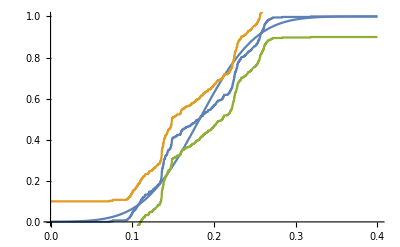

```mathematica
Show[CDF5,CDF6]
```

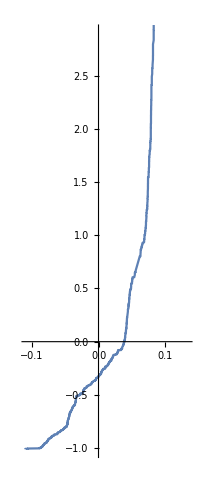

```mathematica
SDrp=Sort[Drp];
Syy=Sort[yy];
QDrp[x_]:=SDrp[[IntegerPart[x*Length[SDrp]]]]
Qyy[x_]:=Syy[[IntegerPart[x*Length[Syy]]]]
ParametricPlot[{QDrp[k]-MeanDrp,Qyy[k]-Meanyy},{k,0,1}]
```

From the above graphs, we can see that the Exponential plot fits nicely for the K-S test, but Drp data does not fit well with normal distribution.

### Problem 3

#### Calculate the mean and variance of the geometric and negative binomial distributions of Section 3.5. Use Mathematica if your analytic tools fail you.

We first compute the mean and variance of the geometric binomial distributions 
mean =  ∑_(k=0)^∞ k*p(1-p)^(k-1)= p ∑_(k=0)^∞ k*(1-p)^(k-1) = p [ⅆ/ⅆp(-∑_(k=0)^∞ (1-p)^k)] = p  ⅆ/ⅆp(-1/p) = 1/p

```mathematica
m[pp_] = ∑_(k=0)^∞ k*pp(1-pp)^(k-1)
```

1/pp

```mathematica
variance[pp_]= Simplify[ ∑_(k=0)^∞ k^2*pp(1-pp)^(k-1)-m[pp]^2]
```

(1-pp)/pp^2

We then compute the mean and variance for the negative binomial distributions

```mathematica
m2[r_,pp_]= Simplify[ ∑_(k=0)^∞ k*({{k-1}, {pp-1}})pp^r(1-pp)^(k-r)]
```

After simplify the expression, we can get that mean = ((1-p)r)/p

```mathematica
variance [r_,pp_] =  Simplify[ ∑_(k=0)^∞ k^2*({{k-1}, {pp-1}})pp^r(1-pp)^(k-r)-m2[r,pp]^2]
```

After simplify the expression, we can get that variance = ((1-p)r)/p^2